Created by: ruebenko on 03-14-2019 13:00:58

### Categorization

Tutorial

Applications

Applications`

FEMAddOns/tutorial/BellAcoustics

Synonyms

### Keywords

bell

acoustics

bell acoustics

bell audio

bell sound

vibration

Structural Mechanics

structural vibration

eigenvalues

eigenmodes

eigenfrequency

Details

# Bell Acoustics

Georgios Varnavides, Wendi Kong,Monica Shifflet, Emily Thai, Hannah von Oldenburg
December 2016

## Introduction

The familiar bell sound is produced by superposition of eigenfrequencies - usually given with respect to the prime (2nd eigenfrequency).

-Graphics-

We can simulate these ‘ideal rations’ inside a decay envelope and produce the following sound.

Model the sounds of a bell.

```mathematica
Clear[sineBank,audioData,sound]
primeFrequency=200;
ratios={0.5,1,1.2,1.5,2.,2.5,2.667,3,4};
decay=Table[If[t<.003,100 t,(1-t/4)^3],{t,0,4-1/44100,1/44100}];
sineBank["ideal"]=Mean[(AudioGenerator[{"Sin",#},4]&/@(primeFrequency ratios))];
audioData["ideal"]=First[AudioData[sineBank["ideal"]]]decay;
sound["ideal"]=ListPlay[audioData["ideal"],SampleRate->44100,PlayRange->All]
```

## Problem statement

There are two convolved effects in bell acoustics. Namely the bell geometry and the material stiffness.
Can we reproduce the sound of a bell using arbitrary geometries?
In particular holding geometry constant (for an easy to fabricate closed-cap cylinder), can we tune materials properties to achieve an aesthetically pleasing bell sound?
Motivation:

Bell casting is a costly process

Traditional bells are usually casted slightly thicker than necessary. They are then turned on a lathe while being tuned simultaneously. This is a wasteful process

Scientific curiosity

## Obtaining eigenfrequencies

### Importing the bell STL file

Import the geometric model and generate a boundary mesh.

```mathematica
Needs["NDSolve`FEM`"]
stlBell=Import[FileNameJoin[{NotebookDirectory[],"SupportFiles","bell.stl"}],"ElementMesh"];
```

Visualize the boundary mesh with boundary regions colored.

```mathematica
rr=Most[Range[0,1,1/(Length[stlBell["BoundaryElementMarkerUnion"]])]];
colors=ColorData["BrightBands"][#]&/@rr;
stlBell["Wireframe"["MeshElementStyle"->(Directive[FaceForm[#],EdgeForm[]]&/@colors)]]
```

-Graphics-

Generate the full mesh.

```mathematica
emesh=ToElementMesh[stlBell,"MeshOrder"->1,"MaxCellMeasure"->.0001]
```

ElementMesh[{{-2.00457,2.00457},{-2.00457,2.00457},{0.0651961,3.9267}},{TetrahedronElement[<66510>]}]

setup a 3D stress operator.

```mathematica
stressOperator[Y_,ν_]:={Inactive[Div][({{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,0,0},{-(Y/(2 (1+ν))),0,0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-((Y ν)/((1-2 ν) (1+ν))),0},{-(Y/(2 (1+ν))),0,0},{0,0,0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-((Y (1-ν))/((1-2 ν) (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,-(Y/(2 (1+ν))),0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-(Y/(2 (1+ν))),0},{-((Y ν)/((1-2 ν) (1+ν))),0,0},{0,0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-((Y (1-ν))/((1-2 ν) (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-(Y/(2 (1+ν)))},{0,-((Y ν)/((1-2 ν) (1+ν))),0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,0,-(Y/(2 (1+ν)))},{0,0,0},{-((Y ν)/((1-2 ν) (1+ν))),0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-((Y (1-ν))/((1-2 ν) (1+ν)))}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]}
```

Inspect the stress operator.

```mathematica
stressOperator[Y,ν]//MatrixForm
```

(({{0,0,-(Y ν)/((1-2 ν) (1+ν))},{0,0,0},{-Y/(2 (1+ν)),0,0}}.w[x,y,z]{x,y,z}Inactive){x,y,z}Inactive+({{0,-(Y ν)/((1-2 ν) (1+ν)),0},{-Y/(2 (1+ν)),0,0},{0,0,0}}.v[x,y,z]{x,y,z}Inactive){x,y,z}Inactive+({{-(Y (1-ν))/((1-2 ν) (1+ν)),0,0},{0,-Y/(2 (1+ν)),0},{0,0,-Y/(2 (1+ν))}}.u[x,y,z]{x,y,z}Inactive){x,y,z}Inactive
({{0,0,0},{0,0,-(Y ν)/((1-2 ν) (1+ν))},{0,-Y/(2 (1+ν)),0}}.w[x,y,z]{x,y,z}Inactive){x,y,z}Inactive+({{0,-Y/(2 (1+ν)),0},{-(Y ν)/((1-2 ν) (1+ν)),0,0},{0,0,0}}.u[x,y,z]{x,y,z}Inactive){x,y,z}Inactive+({{-Y/(2 (1+ν)),0,0},{0,-(Y (1-ν))/((1-2 ν) (1+ν)),0},{0,0,-Y/(2 (1+ν))}}.v[x,y,z]{x,y,z}Inactive){x,y,z}Inactive
({{0,0,0},{0,0,-Y/(2 (1+ν))},{0,-(Y ν)/((1-2 ν) (1+ν)),0}}.v[x,y,z]{x,y,z}Inactive){x,y,z}Inactive+({{0,0,-Y/(2 (1+ν))},{0,0,0},{-(Y ν)/((1-2 ν) (1+ν)),0,0}}.u[x,y,z]{x,y,z}Inactive){x,y,z}Inactive+({{-Y/(2 (1+ν)),0,0},{0,-Y/(2 (1+ν)),0},{0,0,-(Y (1-ν))/((1-2 ν) (1+ν))}}.w[x,y,z]{x,y,z}Inactive){x,y,z}Inactive)

Find the eigenvalues of the unconstraint bell.

```mathematica
{eigenVals,eigenVecs}=Chop[NDEigensystem[{stressOperator[100 ,1/3]},{u,v,w},{x,y,z}∈emesh,30]];
eigenVals
```

{0,0,0,0,0,0,1.62807,1.63274,4.96684,4.98739,9.04334,9.05362,12.4015,12.4047,18.125,22.1537,22.1747,22.2701,26.8664,26.8978,28.054,29.477,29.5349,29.5397,29.6311,43.7809,43.8184,46.1361,46.2046,53.0259}

Note this is a ‘free standing’ bell (i.e. no Dirichlet conditions), meaning that the first 6 eigenfrequencies are zero.

Highlight the 3 rigid body translations and the 3 rotations.

```mathematica
eigenFrequencies["computed"]=Take[Rest[DeleteDuplicates[eigenVals,Abs[#1-#2]<0.05&]/eigenVals[[9]]],9];
TableForm[{ratios,eigenFrequencies["computed"]},TableHeadings->{{"Ideal","Computed"},Automatic},TableAlignments->Center]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
Ideal | ratios |  |  |  |  |  |  |  | 
Computed | 0.327788 | 1. | 1.82074 | 2.49686 | 3.64921 | 4.46032 | 4.48375 | 5.40916 | 5.64826

Visualize the eigenmodes as a wireframe over the undeformed region.

```mathematica
Grid[Riffle[Partition[MapIndexed[Style[StringTemplate["Mode `1`: `2`"][IntegerString[#2[[1]],10,2],ToString@NumberForm[#1,{6,4}]],16,Black]&,Take[eigenVals,{7,14}]],4],Partition[(Show[{
MeshRegion[emesh],ElementMeshDeformation[emesh,eigenVecs[[#]],"ScalingFactor"->1/2]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]}]&/@Range[7,14]),4]]]
```

-Graphics-

Listen to the computed sound of the bell.

```mathematica
sineBank["computed"]=Mean[(AudioGenerator[{"Sin",#},4]&/@(primeFrequency eigenFrequencies["computed"]))];
audioData["computed"]=First[AudioData[sineBank["computed"]]]decay;
sound["computed"]=ListPlay[audioData["computed"],SampleRate->44100,PlayRange->All]
```

## Cylinder Eigenfrequencies

Generate and visualize the mesh of a hollowed cylinder.

```mathematica
Clear[cylinder]
cylinder[inner_:1.5,outer_:2,height_:4,capThickness_:0.25]:=ImplicitRegion[inner^2≤x^2+y^2≤outer^2&&0≤z≤(height-capThickness)||x^2+y^2≤outer^2&&(height-capThickness)<=z≤height,{x,y,z}];
cylmesh=ToElementMesh[cylinder[],"MeshOrder"->1,"MaxCellMeasure"->.01];
cylmesh["Wireframe"]
```

-Graphics3D-

### Materials Properties

There’s a number of ways we can vary materials properties across the simple cylinder geometry. Perhaps the simplest is to vary the value as a function of height alone.

Set up a continuous material modulus.

```mathematica
modulus["continuous"][Y0_,Y1_,height_:4]:=Y0 +(Y1-Y0) z/height
```

Set up a discrete material modulus.

```mathematica
modulus["discrete"][Y0_,Y1_,height_:4,increments_:1]:=Y0 +(Y1-Y0) Floor[z /increments]/height increments
```

Set up a piecewise material modulus.

```mathematica
modulus["piecewise"][moduli_,ranges_]:=Module[{zranges},
zranges=#[[1]]<z<#[[2]]&/@Partition[ranges,2,1];
Piecewise[Thread[{moduli,zranges}]]]
```

Visualize the various material moduli.

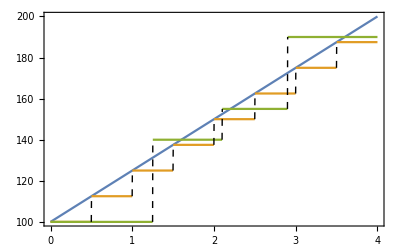

```mathematica
Plot[{modulus["continuous"][100,200,4],modulus["discrete"][100,200,4,.5],modulus["piecewise"][{100,140,155,190},{0,1.25,2.1,2.9,4}]},{z,0,4},PlotRange->{Automatic,200},ExclusionsStyle->Dashing[Small],Frame->True]
```

Compute the eigensystem for the continuous material modulus.

```mathematica
{eigenValsCyl["continuous"],eigenVecsCyl["continuous"]}=Chop@NDEigensystem[stressOperator[modulus["continuous"][100,200,4],1/3],{u,v,w},{x,y,z}∈cylmesh,30];
```

Compute the eigensystem for the discrete material modulus.

```mathematica
{eigenValsCyl["discrete"],eigenVecsCyl["discrete"]}=Chop@NDEigensystem[stressOperator[modulus["discrete"][100,200,4,.5],1/3],{u,v,w},{x,y,z}∈cylmesh,30];
```

Compute the eigensystem for the piecewise material modulus.

```mathematica
{eigenValsCyl["piecewise"],eigenVecsCyl["piecewise"]}=Chop@NDEigensystem[stressOperator[modulus["piecewise"][{100,140,155,190},{0,1.25,2.1,2.9,4}],1/3],{u,v,w},{x,y,z}∈cylmesh,30];
```

Write a helper function to extract the eigen frequencies.

```mathematica
eigenFrequencies[type_]:=Take[Rest[DeleteDuplicates[eigenValsCyl[type],Abs[#1-#2]<3&]/eigenValsCyl[type][[9]]],9];
```

Extract the eigenfrequencies for the various material moduli.

```mathematica
TableForm[Prepend[eigenFrequencies/@{"computed","continuous","discrete","piecewise"},ratios],TableHeadings->{{"Ideal","Computed Bell","Continuous","Discrete","Piecewise"},Automatic},TableAlignments->Center]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
Ideal | 0.5 | 1 | 1.2 | 1.5 | 2. | 2.5 | 2.667 | 3 | 4
Computed Bell | 0.327788 | 1. | 1.82074 | 2.49686 | 3.64921 | 4.46032 | 4.48375 | 5.40916 | 5.64826
Continuous | 0.244221 | 1. | 1.29654 | 1.42613 | 1.58514 | 1.76173 | 2.33676 | 2.47606 | 2.68471
Discrete | 0.24311 | 1. | 1.29604 | 1.5793 | 1.76133 | 2.33058 | 2.4749 | 2.68425 | 2.8125
Piecewise | 0.234368 | 1. | 1.27496 | 1.5463 | 1.74119 | 2.28237 | 2.47632 | 2.6519 | 2.77878

## Minimization

Restricting ourselves to the easy-to-fabricate piecewise model above, we can define a minimization procedure based on a least squares metric with the ideal ratios. The variable space is quite large (thicknesses and Young’s modulus for each slab), making it hard to visualize. A dummy example minimization of a two section cylinder is shown below.

-Graphics-

## Experimental Results

Minimization in a higher dimensional space, yielded the following parameters to try experimentally:

-Graphics-

### Casting and Machining

Young’s moduli were matched to different Bronze alloys (varying percentages of tin)

Rings were cast, and cut close to the inner/outer dimensions using the waterjet

Rings were turned on the lathe to exact dimensions

### Diffusion bonding

Rings were bonded using diffusion bonding to avoid sharp interfaces (source of reflection). In diffusion bonding, two metal pieces are joined together and kept at high pressure and temperature for a long time, such that atoms of the two metals interdiffuse and the two pieces are then joined.

## Acoustic Comparison

```mathematica
trimmedAudio=;
```

```mathematica
audioPlot=AudioPlot[trimmedAudio,FillingStyle->Red,PlotStyle->Black,ImageSize->750,FrameStyle->Directive[Black,Thick],BaseStyle->14,PlotLayout->"Averaged",FrameLabel->{"Time [seconds]","Normalized amplitude"},AspectRatio->1/5]
```

Extracting the audio data.

```mathematica
amplitudes=AudioData[trimmedAudio][[1]];
times=Range[Length[amplitudes]]/44100;
ListPlot[Transpose[{times,amplitudes}],PlotRange->All, Frame-> True,BaseStyle->14,FrameStyle->Directive[Black,Thick],PlotStyle->{Red,Thick},FrameLabel-> {"Time (seconds)","Audio Amplitude"},ImageSize->750]
```

Taking the Fast Fourier Transform.

```mathematica
fft=Take[Abs[Fourier[amplitudes]],Round[Length[amplitudes]/2]];
ListLinePlot[fft,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->Red]
```

Find the first couple of peaks.

```mathematica
peaks=Rest@FindPeaks[fft,150,Automatic];
image[8]=ListLinePlot[fft, Epilog-> {Blue,PointSize[0.01],Point[peaks]},PlotRange->{{0,20000},All},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->Red,FrameLabel-> {"Frequency (Hertz)","Mode Amplitude"},BaseStyle->14,ImageSize->750]
```

Compute the partial frequencies.

```mathematica
frequencies =N@ Range[0,Length[amplitudes]-1]44100/Length[amplitudes];
{partialFrequencies,eigenAmplitudes}=Transpose[Thread[{Take[frequencies,Round[Length[amplitudes]/2]],fft}][[First/@peaks]]];
```

Compute the eigen ratios.

```mathematica
eigenRatios=Take[partialFrequencies,8]/partialFrequencies[[2]]
```

```mathematica
ratios={0.5,1,1.2,1.5,2,2.5,2.667,3};
```

```mathematica
Abs[eigenRatios-ratios]/ratios 100
```

Generate the audio from the prime frequency.

```mathematica
primeFrequency=partialFrequencies[[2]];
decay=Table[If[t<.003,100 t,(1-t/times[[-1]])^3],{t,0,times[[-1]]-1/44100,1/44100}];
sineBank=Mean[(AudioGenerator[{"Sin",#},times[[-1]]]&/@(primeFrequency eigenRatios))];
audioData=First[AudioData[sineBank]]decay;
res=ListPlay[audioData,SampleRate->44100,PlayRange->All]
```

Putting it all together.

```mathematica
ListPlot[Transpose[{frequencies,Abs[Fourier[amplitudes]]}][[1;;Round[Length[amplitudes]/2]]], Frame-> True,FrameStyle->Directive[Black,Thick],BaseStyle->14,Filling->0,PlotStyle->{PointSize[0.01], Blue},FrameLabel-> {"Frequency (Hertz)","Mode Amplitude"},PlotRange->All,
Epilog->{Inset[Image[audioPlot,ImageSize->500],{14000,11}],Dashed,Red,Thickness[.0025],(Line[{{#,0},{#,5}}]&/@partialFrequencies[[;;8]])},ImageSize->750,AspectRatio->1/2]
```

More About

Related Tutorials

Related Wolfram Training Courses